## Configuration

```mathematica
Quiet[Needs["HypExp`"]];
Quiet[NotebookEvaluate["/Users/Matt/Documents/Research/MIW_mathematica/MIW_header_file.nb"]];

(* 

This notebook calculates the order(alpha_s tau) rate for each operator combination, in each region, and matches them onto the necessary soft operators

*)
```

Epsilon divergences for perp integrals with non-zero masses

div A0: 2/((D-4) π)

div A1: 0

div A00: m10/((D-4) π)

div A11: 0

div A001: 0

div A111: 0

div A0000: m10^2/(4 (D-4) π)

div A0011: 0

div A1111: 0

div A00001: 0

div A00111: 0

div A11111: 0

div B0: 0

div B1: 0

div B00: 1/((D-4) π)

div B11: 0

div B001: -1/(2 (D-4) π)

div B111: 0

div B0000: (3 (m10+m20)-p10)/(12 (D-4) π)

div B0011: 1/(3 (D-4) π)

div B1111: 0

div B00001: (-2 m10-4 m20+p10)/(24 (D-4) π)

div B00111: -1/(4 (D-4) π)

div B11111: 0

```mathematica
timeLimit=0.5;(* in minutes *)(* set this higher overnight *)
timeLimit=timeLimit*60;
$LimitTo4//myPrint
turnOffConditional[];
```

$LimitTo4=False

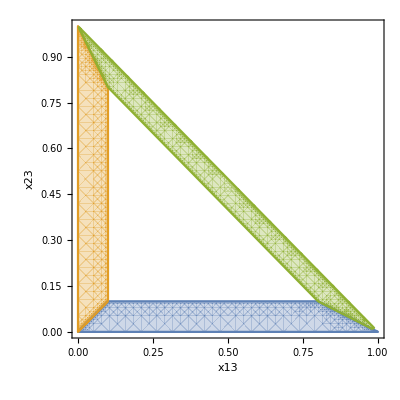

```mathematica
$Assumptions=0<eps<1/10 && 0<M<Q && 0<p1m<Q&&0<p1p<Q&&0<p2m<Q&&0<p2p<Q&&0<qm<Q&&0<qp<Q&&km∈Reals&&0≤ x≤ 1&&0≤ y≤ 1&&0≤ z≤ 1&&0≤ w≤ 1/3&&p3p∈Reals&&p3m∈Reals&&p4p∈Reals&&p4m∈Reals&&lambda∈Reals&&Q>0&&1/3>tau>0&&muMS>0&&1/3>tau>0&&0<qhatp<1&&0<qhatm<1;

replSingVarPlus[e_]:=e/.PlusDistribution[a_*HeavisideTheta[b_]]:>HeavisideTheta[b-beta]a+DiracDelta[b-beta]Integrate[a,{tau,1,tau}]/.PlusDistribution[a_]:>HeavisideTheta[tau-beta]a+DiracDelta[tau-beta]Integrate[a,{tau,1,tau}];

expLogs[e_]:=e//.Log[a_/b_]:>Log[a]-Log[b]//.Log[a_*b_]:>Log[a]+Log[b]/.Log[a_^n_]:>  n*Log[a];
dimensionalize[e_]:=e/.qhatm->qm/Q/.qhatp->qp/Q/.p1hatm->p1m/Q/.p1hatp->p1p/Q/.p2hatm->p2m/Q/.p2hatp->p2p/Q;


(* kinematics for p1m=0 *)
regBkinematics[e_]:=dimensionalize[e]/.Vperp[p2]->-Vperp[q]/.Vperp[p1]->0/.p1m->Q*p1hatm/.p2m->Q*p2hatm/.qm->Q*qhatm/.p1p->Q*p1hatp/.p2p->Q*p2hatp/.qp->Q*qhatp/.p2hatm->1-qhatm/.p2hatp->qhatp*qhatm/(1-qhatm)/.p1hatp->qhatm*(1-qhatp/(1-qhatm))/.p1hatm->0/.qhatp->x23*(1-qhatm)/.qhatm->x13/(1-x23);

(* kinematics for p2m=0 *)
regAkinematics[e_]:=dimensionalize[e]/.Vperp[p1]->-Vperp[q]/.Vperp[p2]->0/.p1m->Q*p1hatm/.p2m->Q*p2hatm/.qm->Q*qhatm/.p1p->Q*p1hatp/.p2p->Q*p2hatp/.qp->Q*qhatp/.p1hatm->1-qhatm/.p2hatp->(1-qhatp/(1-qhatm))/.p1hatp->qhatp*qhatm/(1-qhatm)/.p2hatm->0/.qhatp->x13*(1-qhatm)/.qhatm->x23/(1-x13);

(* kinematics for qm=0 *)
regCkinematics[e_]:=dimensionalize[e]/.Vperp[p2]->-Vperp[p1]/.Vperp[q]->0/.p1m->Q*p1hatm/.p2m->Q*p2hatm/.qm->Q*qhatm/.p1p->Q*p1hatp/.p2p->Q*p2hatp/.qp->Q*qhatp/.p2hatm->1-p1hatm/.p2hatp->p1hatp*p1hatm/(1-p1hatm)/.qhatp->qhatm*(1-p1hatp/(1-p1hatm))/.qhatm->0/.p1hatp->(1-p1hatm)(1-x13/p1hatm)/.p1hatm->x13/(x13+x23);

(* options *)
onlyLO=True;
onlyNLO=False;
doCheckLeftoverIntegrals=False;

prefac=g^2*Cf;

phasespaceA=0;
phasespaceB=0;
phasespaceC=0;

(* 
  angularity definitions in the three regions of Dalitz-space 
*)
fA[x13_,x23_,a_]:=(x13 (x13+x23-1) (-x23/(x13 (x13+x23-1)))^(a/2)-x13 x23 (-(x13+x23-1)/(x13 x23))^(a/2))/(x13-1)
fB[x13_,x23_,a_]:=(x23 (x13+x23-1) (-x13/(x23 (x13+x23-1)))^(a/2)-x13 x23 (-(x13+x23-1)/(x13 x23))^(a/2))/(x23-1)
fC[x13_,x23_,a_]:=-((x13+x23-1) (x23 (-x13/(x23 (x13+x23-1)))^(a/2)+x13 (-x23/(x13 (x13+x23-1)))^(a/2)))/(x13+x23)
(* plot the thing *)
tautau=0.1;
aa=0;
RegionPlot[{2x13+x23<1&&x13+x23<1&&x23>x13&&0<fA[x13,x23,aa]<tautau,x13+2x23<1&&x13+x23<1&&x13>x23&&0<fB[x13,x23,aa]<tautau,2x13+x23>1&&x13+2x23>1&&x13+x23<1&&0<fC[x13,x23,aa]<tautau},{x23,0,1},{x13,0,1},AxesLabel-> {x13,x23},MaxRecursion->5]

Unprotect[Tr];
Tr/:Tr[0]:=0;
Protect[Tr];

spinSumHornig=MTD[alpha,beta](MTD[mu,nu]-FVD[n+nb,mu]FVD[n+nb,nu]/4);
spinSumTranseverse=MTD[alpha,beta](MTD[mu,nu]-FVD[nb,mu]FVD[n,nu]/2-FVD[n,mu]FVD[nb,nu]/2);
spinSumSimple=MTD[alpha,beta](MTD[mu,nu]);

spinSum=spinSumHornig;

phaseSpacePrefac=1/(64*Pi^2)*(4*Pi/(Q^2))^(+eps)/(Gamma[2-eps]);
c2=1+alphaMS*Cf*(-Log[(-Q^2+I*delta)/muMS^2]^2+3*Log[(-Q^2+I*delta)/muMS^2]+Pi^2/6-8)/(4*Pi);
Z2=1+Cf*alphaMS(2/eps^2+(-2*Log[(-Q^2+I*delta)/muMS^2]+3)/eps)/(4*Pi);
```

## Expressions for Integration Regions

### Phase Space Integrals

#### A -- Sideways Integration (x-first)

```mathematica
(* try integrating x first, then y *)

(*
regAs1=Integrate[x^(n-1+eps)(1-x-y)^(eps),{x,y,1-2*y}];
regAs2=Integrate[%*y^(m-1+eps),{y,0,tau}];
regAs3=Series[%,{tau,0,2}]//Normal;
*)

(* it worked but the output is HUGE! Almost 57000 terms long *)

(* instead of keeping the huge result, we'll store the 4x4 {n,m} elements that are necessary for usual calculations *)
(* remember, the epsilons here are IR regulators, so negative. Later, use /.eps->negeps/.negeps->-eps to revert back to regular epsilons *)

regA00=-Pi^2/6+1/(2*ϵ^2)-2*τ-Log[τ]^2/2; 
regA01=τ*(1-Log[τ]);
regA02=0;
regA03=0;

regA10=-2+ϵ^(-1)-3*τ+Log[τ];
regA11=τ;
regA12=0;
regA13=0;

regA20=-1+1/(2*ϵ)-2*τ+Log[τ]/2;
regA21=τ/2;
regA22=0;
regA23=0;

regA30=-13/18+1/(3*ϵ)-2*τ+Log[τ]/3;
regA31=τ/3;
regA32=0;
regA33=0;
```

```mathematica
(*
Integrate[x^(0-1+eps)(1-x-y)^(eps),{x,y,1-2*y}]
Integrate[%*y^(0-1+eps),{y,0,tau}]
Series[%,{tau,0,4}]//Normal

Series[%,{tau,0,1}]//Normal
Series[%,{eps,0,0}]//Normal
Series[%,{tau,0,1}]//Normal
*)
```

#### B -- Vertical Integration (y-first)

```mathematica
(* summary *)

regB00=regA00;
regB01=regA10;
regB02=regA20;
regB03=regA30;

regB10=regA01;
regB11=regA11;
regB12=regA21;
regB13=regA31;

regB20=regA02;
regB21=regA12;
regB22=regA22;
regB23=regA32;

regB30=regA03;
regB31=regA13;
regB32=regA23;
regB33=regA33;
```

```mathematica
(*
Integrate[y^(m-1+eps)(1-x-y)^(eps),{y,x,1-2*x}]
Integrate[%*x^(n-1+eps),{x,0,tau}]
regBlong=Series[%,{tau,0,2}]//Normal
*)

(* this is equivalent to the region A integration, but with n interchanged with m *)
```

#### C -- Sideways Integration (x-first)

```mathematica
(* summary *)

(* it looks like I only need to know the result for c02, c11, and c20, so let's just do those *)

(* remember, the epsilons here are IR regulators, so negative. Later, use /.eps->negeps/.negeps->-eps to revert back to regular epsilons *)

regC00=τ*(2-2*Log[τ]);
regC01=τ-τ*Log[τ];
regC02=-(τ*Log[τ]);
regC03=τ*(-1/2-Log[τ]);

regC10=τ*(1-Log[τ]);
regC11=τ;
regC12=τ/2;
regC13=τ/3;

regC20=-(τ*Log[τ]);
regC21=τ/2;
regC22=τ/6;
regC23=τ/12;

regC30=-(τ*(1+2*Log[τ]))/2;
regC31=τ/3;
regC32=τ/12;
regC33=τ/30;
```

```mathematica
(* convert integrals from y to u=1-x-y *)
(* then the integration region has the same form as region A so we can try the sideways integration again *)

(*nn=1;
mm=1;

regCs02i=Integrate[x^(nn-1+eps)(1-x-u)^(mm-1+eps),{x,u,1-2*u}]

%/.Hypergeometric2F1Regularized[a_,b_,c_,d_]:>HypExp[Hypergeometric2F1Regularized[a,b,c,d],eps,2]/.Hypergeometric2F1[a_,b_,c_,d_]:>HypExp[Hypergeometric2F1[a,b,c,d],eps,2]/.Beta[z_,a_,b_]:>(z^a/a)*HypExp[Hypergeometric2F1[a,1-b,1+a,z],eps,2]

regCs02ii=Integrate[%*u^eps,{u,0,tau}]
regCs02=Series[%,{tau,0,2}];
regCs02=Series[%,{tau,0,1}]//Normal;
regCs02=Series[%,{eps,0,0}]//Normal
regCsnnmm=Series[%,{tau,0,1}]//Normal
regCsnnmm//InputForm*)
```

#### Overall

```mathematica
int00=regA00+regB00+regC00;
int01=regA01+regB01+regC01;
int02=regA02+regB02+regC02;
int03=regA03+regB03+regC03;

int10=regA10+regB10+regC10;
int11=regA11+regB11+regC11;
int12=regA12+regB12+regC12;
int13=regA13+regB13+regC13;

int20=regA20+regB20+regC20;
int21=regA21+regB21+regC21;
int22=regA22+regB22+regC22;
int23=regA23+regB23+regC23;

int30=regA30+regB30+regC30;
int31=regA31+regB31+regC31;
int32=regA32+regB32+regC32;
int33=regA33+regB33+regC33;
```

## Subsubleading Order

```mathematica
(* Recall the factorization formula : *)

(* int d_phi O_2^i Mhat O_2^j = int_0^tau C_s^ijk S^k + tau*int_0^tau C_Stau^ij S^0 *)
```

### Contributions from A-type operators

```mathematica
ampO20a=-I*g*Ta*SpinorUBar[p1].(  (2*FVD[p1,alpha]+GAD[alpha].GSD[q])/(2*SPD[p1,q])-FVD[nb,alpha]/SPD[nb,q]).Phatnb.GAD[mu].Phatnb.SpinorV[p2]//DeltaDef;
ampO21a=-I*g*Ta*SpinorUBar[p1].(Vperp[GAD[rho]].(GSD[nb]/2).GAD[mu].Phatnb-Phatnb.GAD[mu].(GSD[n]/2).Vperp[GAD[rho]]).SpinorV[p2]*Deltabarq[alpha,rho]/Q//DeltaDef;
ampO22a1=I*g*Ta*SpinorUBar[p1].(Phatnb.GAD[mu].Phatnb.Vperp[GAD[rho]].Vperp[GAD[sigma]]/qhatm).SpinorV[p2]*FVD[q,rho]*Deltabarq[alpha,sigma]/Q^2//DeltaDef;
ampO22a2=I*g*Ta*SpinorUBar[p1].(Vperp[GAD[rho]].(GSD[nb]/2).GAD[mu].(GSD[n]/2).Vperp[GAD[sigma]]/p1hatm).SpinorV[p2]*FVD[q,rho]*Deltabarq[alpha,sigma]/Q^2//DeltaDef;

ampDagO20a=I*g*Tb*SpinorVBar[p2].Phatn.GAD[nu].Phatn.(  (2*FVD[p1,beta]+GSD[q].GAD[beta])/(2*SPD[p1,q])-FVD[nb,beta]/SPD[nb,q]).SpinorU[p1]//DeltaDef;
ampDagO21a=I*g*Tb*SpinorVBar[p2].(Phatn.GAD[nu].(GSD[nb]/2).Vperp[GAD[phi]]-Vperp[GAD[phi]].(GSD[n]/2).GAD[nu].Phatn).SpinorU[p1]*Deltabarq[beta,phi]/Q//DeltaDef;
ampDagO22a1=-I*g*Tb*SpinorVBar[p2].(Vperp[GAD[phi]].Vperp[GAD[psi]].Phatn.GAD[nu].Phatn/qhatm).SpinorU[p1]*FVD[q,psi]*Deltabarq[beta,phi]/Q^2//DeltaDef;
ampDagO22a2=-I*g*Tb*SpinorVBar[p2].(Vperp[GAD[phi]].(GSD[n]/2).GAD[nu].(GSD[nb]/2).Vperp[GAD[psi]]/p1hatm).SpinorU[p1]*FVD[q,psi]*Deltabarq[beta,phi]/Q^2//DeltaDef;
```

#### < O20a | O20a >

```mathematica
ampO20aO20a=GSD[p2].ampDagO20a.GSD[p1].ampO20a*spinSum/.SpinorUBar[p1].a_:>a/.a_ .SpinorU[p1]:>a/.SpinorVBar[p2].a_:>a/.a_ .SpinorV[p2]:>a;

%//DiracSimplify//FCE;
%/.Ta*Tb->Cf//PhatDef//lcCompAll;
%/.Vperp[p1]->-Vperp[q]/.Vperp[p2]->0//Contract//DiracSimplify//FCE;
%//gPerpDef;
dTraceO20aO20a=(Tr[%]//FCE//DiracSimplify//FCE); 

dTraceO20aO20a//regAkinematics;
%//Simplify;
%/.D->4-2*eps//Simplify;
O20aO20afinite=Series[%,{eps,0,1}]//Normal;

krabbyO20aO20a=O20aO20afinite/.eps->negeps/.negeps->-eps   (* flip the epsilon here *)

(* 
from here recognize c00, c01, c02, c10, c11, c12, c20,c21,c22,etc. 
*)
O20aO20a00=SeriesCoefficient[krabbyO20aO20a*x13*x23,{x23,0,0},{x13,0,0}];
O20aO20a10=SeriesCoefficient[krabbyO20aO20a*x13*x23,{x23,0,1},{x13,0,0}];
O20aO20a20=SeriesCoefficient[krabbyO20aO20a*x13*x23,{x23,0,2},{x13,0,0}];
O20aO20a30=SeriesCoefficient[krabbyO20aO20a*x13*x23,{x23,0,3},{x13,0,0}];

O20aO20a01=SeriesCoefficient[krabbyO20aO20a*x13*x23,{x23,0,0},{x13,0,1}];
O20aO20a11=SeriesCoefficient[krabbyO20aO20a*x13*x23,{x23,0,1},{x13,0,1}];
O20aO20a21=SeriesCoefficient[krabbyO20aO20a*x13*x23,{x23,0,2},{x13,0,1}];
O20aO20a31=SeriesCoefficient[krabbyO20aO20a*x13*x23,{x23,0,3},{x13,0,1}];

O20aO20a02=SeriesCoefficient[krabbyO20aO20a*x13*x23,{x23,0,0},{x13,0,2}];
O20aO20a12=SeriesCoefficient[krabbyO20aO20a*x13*x23,{x23,0,1},{x13,0,2}];
O20aO20a22=SeriesCoefficient[krabbyO20aO20a*x13*x23,{x23,0,2},{x13,0,2}];
O20aO20a32=SeriesCoefficient[krabbyO20aO20a*x13*x23,{x23,0,3},{x13,0,2}];

O20aO20a03=SeriesCoefficient[krabbyO20aO20a*x13*x23,{x23,0,0},{x13,0,3}];
O20aO20a13=SeriesCoefficient[krabbyO20aO20a*x13*x23,{x23,0,1},{x13,0,3}];
O20aO20a23=SeriesCoefficient[krabbyO20aO20a*x13*x23,{x23,0,2},{x13,0,3}];
O20aO20a33=SeriesCoefficient[krabbyO20aO20a*x13*x23,{x23,0,3},{x13,0,3}];

coeffArrO20aO20a={{O20aO20a00,O20aO20a01,O20aO20a02,O20aO20a03},{O20aO20a10,O20aO20a11,O20aO20a12,O20aO20a13},{O20aO20a20,O20aO20a21,O20aO20a22,O20aO20a23},{O20aO20a30,O20aO20a31,O20aO20a32,O20aO20a33}}
checksumO20aO20a=krabbyO20aO20a*x13*x23-({1,x23,x23^2,x23^3}.coeffArrO20aO20a.{1,x13,x13^2,x13^3})//FullSimplify


(* contribution from region A *)

totalO20aO20a=0;
totalO20aO20a+=O20aO20a00*regA00+O20aO20a01*regA01+O20aO20a02*regA02+O20aO20a03*regA03;
totalO20aO20a+=O20aO20a10*regA10+O20aO20a11*regA11+O20aO20a12*regA12+O20aO20a13*regA13;
totalO20aO20a+=O20aO20a20*regA20+O20aO20a21*regA21+O20aO20a22*regA22+O20aO20a23*regA23;
totalO20aO20a+=O20aO20a30*regA30+O20aO20a31*regA31+O20aO20a32*regA32+O20aO20a33*regA33;
totalO20aO20a=totalO20aO20a/.eps->negeps/.negeps->-eps//FullSimplify  (* and flip the epsilon back here *)

(* the factor of two comes from the equal contribution in the B sector that must be included since O20 doesnt set the gluon quantum number *)
contributionO20aO20a=1*(1/Z2)*ComplexConjugate[1/Z2]+2*phaseSpacePrefac*totalO20aO20a; 

%/.g->Sqrt[4*Pi*alphaMS*(Exp[EulerGamma]muMS^2/(4Pi) )^eps];
Series[%,{alphaMS,0,1}]//Normal;
Series[%,{eps,0,0}]//Normal;
contributionO20aO20a=%//Expand
```

(16 g^2 ϵ C_F (x13^2+x13 x23-2 x13+x23^2-x23+1))/(x13 x23)+(8 g^2 C_F (2 x13^2+2 x13 x23-4 x13+x23^2-2 x23+2))/(x13 x23)

(16 C_F g^2+16 C_F ϵ g^2 | -32 C_F g^2-32 C_F ϵ g^2 | 16 C_F g^2+16 C_F ϵ g^2 | 0
-16 C_F g^2-16 C_F ϵ g^2 | 16 C_F g^2+16 C_F ϵ g^2 | 0 | 0
8 C_F g^2+16 C_F ϵ g^2 | 0 | 0 | 0
0 | 0 | 0 | 0)

0

(4 g^2 C_F (3 ϵ^2 log(τ) (8 τ+(2-8 τ) ϵ+2 (ϵ-1) log(τ)-3)+ϵ (2 ϵ (6 τ (2 ϵ-1)+(π^2-6) (ϵ-1))+3)+6))/(3 ϵ^2)

-(2 τ C_F α_OverBar[MS])/π-(C_F α_OverBar[MS] log^2(τ))/π+(4 τ C_F α_OverBar[MS] log(τ))/π-(3 C_F α_OverBar[MS] log(τ))/(2 π)-5/12 π C_F α_OverBar[MS]+(7 C_F α_OverBar[MS])/(2 π)+(C_F α_OverBar[MS] log(1/Q^2))/(π ϵ)+(C_F α_OverBar[MS] log^2(1/Q^2))/(2 π)+(3 C_F α_OverBar[MS] log(1/Q^2))/(2 π)+(C_F α_OverBar[MS] log((-Q^2-ⅈ δ)/μ_OverBar[MS]^2))/(2 π ϵ)+(C_F α_OverBar[MS] log((-Q^2+ⅈ δ)/μ_OverBar[MS]^2))/(2 π ϵ)+(C_F α_OverBar[MS] log(1/Q^2) log(μ_OverBar[MS]^2))/π+(C_F α_OverBar[MS] log(μ_OverBar[MS]^2))/(π ϵ)+(C_F α_OverBar[MS] log^2(μ_OverBar[MS]^2))/(2 π)+(3 C_F α_OverBar[MS] log(μ_OverBar[MS]^2))/(2 π)+1

```mathematica
contributionO20aO20a/.alphaMS->alphabar*2*Pi/Cf//Expand
%//expLogs
%/.Log[-Q^2+I*delta]->2Log[Q]+I*Pi/.Log[-Q^2-I*delta]->2Log[Q]-I*Pi
finalO20aO20a=Series[%,{tau,0,1}]//Normal//Expand
```

-4 τ ᾱ-2 ᾱ log^2(τ)+8 τ ᾱ log(τ)-3 ᾱ log(τ)-(5 π^2 ᾱ)/6+7 ᾱ+(ᾱ log((-Q^2-ⅈ δ)/μ_OverBar[MS]^2))/ϵ+(ᾱ log((-Q^2+ⅈ δ)/μ_OverBar[MS]^2))/ϵ+2 ᾱ log(1/Q^2) log(μ_OverBar[MS]^2)+(2 ᾱ log(μ_OverBar[MS]^2))/ϵ+ᾱ log^2(μ_OverBar[MS]^2)+3 ᾱ log(μ_OverBar[MS]^2)+(2 ᾱ log(1/Q^2))/ϵ+ᾱ log^2(1/Q^2)+3 ᾱ log(1/Q^2)+1

-4 τ ᾱ-2 ᾱ log^2(τ)+8 τ ᾱ log(τ)-3 ᾱ log(τ)-(5 π^2 ᾱ)/6+7 ᾱ+(ᾱ (-2 log(μ_OverBar[MS])+log(-Q^2-ⅈ δ)))/ϵ+(ᾱ (-2 log(μ_OverBar[MS])+log(-Q^2+ⅈ δ)))/ϵ-8 ᾱ log(Q) log(μ_OverBar[MS])+(4 ᾱ log(μ_OverBar[MS]))/ϵ+4 ᾱ log^2(μ_OverBar[MS])+6 ᾱ log(μ_OverBar[MS])-(4 ᾱ log(Q))/ϵ+4 ᾱ log^2(Q)-6 ᾱ log(Q)+1

-4 τ ᾱ-2 ᾱ log^2(τ)+8 τ ᾱ log(τ)-3 ᾱ log(τ)-(5 π^2 ᾱ)/6+7 ᾱ+(ᾱ (-2 log(μ_OverBar[MS])+2 log(Q)-ⅈ π))/ϵ+(ᾱ (-2 log(μ_OverBar[MS])+2 log(Q)+ⅈ π))/ϵ-8 ᾱ log(Q) log(μ_OverBar[MS])+(4 ᾱ log(μ_OverBar[MS]))/ϵ+4 ᾱ log^2(μ_OverBar[MS])+6 ᾱ log(μ_OverBar[MS])-(4 ᾱ log(Q))/ϵ+4 ᾱ log^2(Q)-6 ᾱ log(Q)+1

-4 τ ᾱ-2 ᾱ log^2(τ)+8 τ ᾱ log(τ)-3 ᾱ log(τ)-(5 π^2 ᾱ)/6+7 ᾱ-8 ᾱ log(Q) log(μ_OverBar[MS])+4 ᾱ log^2(μ_OverBar[MS])+6 ᾱ log(μ_OverBar[MS])+4 ᾱ log^2(Q)-6 ᾱ log(Q)+1

```mathematica
intSoft0=1+alphabar*(Pi^2/6-Log[tau^2*Q^2/muMS^2]^2)
diffCS0=DiracDelta[tau-delta](1+alphabar*(J+J1*Log[Q/muMS]+J2*Log[Q^2/muMS^2]^2))+alphabar*(  k*PlusDistribution[1/tau]+k1*PlusDistribution[Log[tau*Q^2/muMS^2]/tau] )
(intSoft0/.tau->tau-t)*((diffCS0//replSingVarPlus)/.tau->t)
Series[%,{alphabar,0,1}]//Normal
rate=Integrate[%,{t,0,tau},Assumptions->delta>0&&0<beta<tau]/.delta->0/.beta->0/.HeavisideTheta[tau]->1
```

ᾱ (π^2/6-log^2((Q^2 τ^2)/μ_OverBar[MS]^2))+1

τ-δ (ᾱ (J+J1 log(Q/μ_OverBar[MS])+J2 log^2(Q^2/μ_OverBar[MS]^2))+1)+ᾱ (k (1/τ)_++k1 ((log((Q^2 τ)/μ_OverBar[MS]^2))/τ)_+)

(ᾱ (π^2/6-log^2((Q^2 (τ-t)^2)/μ_OverBar[MS]^2))+1) (ᾱ (k (log(t) t-β+(t-β)/t)+k1 (1/2 log(t) t-β log((Q^4 t)/μ_OverBar[MS]^4)+(t-β log((Q^2 t)/μ_OverBar[MS]^2))/t))+t-δ (ᾱ (J+J1 log(Q/μ_OverBar[MS])+J2 log^2(Q^2/μ_OverBar[MS]^2))+1))

ᾱ (J t-δ+J1 t-δ log(Q/μ_OverBar[MS])+J2 t-δ log^2(Q^2/μ_OverBar[MS]^2)+k log(t) t-β+1/2 k1 log(t) t-β log((Q^4 t)/μ_OverBar[MS]^4)-t-δ log^2((Q^2 (τ-t)^2)/μ_OverBar[MS]^2)+1/6 π^2 t-δ+(k t-β)/t+(k1 t-β log((Q^2 t)/μ_OverBar[MS]^2))/t)+t-δ

1/6 (ᾱ (6 J+6 J1 log(Q/μ_OverBar[MS])+6 J2 log^2(Q^2/μ_OverBar[MS]^2)-6 log^2((Q^2 τ^2)/μ_OverBar[MS]^2)+π^2)+3 ᾱ log(τ) (2 k+k1 log((Q^4 τ)/μ_OverBar[MS]^4))+6)

```mathematica
Series[finalO20aO20a,{tau,0,0}]//Normal
%-rate//Expand//expLogs//Expand

%/.J2->2
%/.J1->-6
%/.k1->4
%/.k->-3
%/.J->7-6Pi^2/6//Expand
```

-2 ᾱ log^2(τ)-3 ᾱ log(τ)-(5 π^2 ᾱ)/6+7 ᾱ-8 ᾱ log(Q) log(μ_OverBar[MS])+4 ᾱ log^2(μ_OverBar[MS])+6 ᾱ log(μ_OverBar[MS])+4 ᾱ log^2(Q)-6 ᾱ log(Q)+1

2 ᾱ log^2(τ)-3 ᾱ log(τ)-π^2 ᾱ+7 ᾱ-J ᾱ+J1 ᾱ log(μ_OverBar[MS])-J1 ᾱ log(Q)+8 J2 ᾱ log(Q) log(μ_OverBar[MS])-4 J2 ᾱ log^2(μ_OverBar[MS])-4 J2 ᾱ log^2(Q)-k ᾱ log(τ)-1/2 k1 ᾱ log^2(τ)+2 k1 ᾱ log(τ) log(μ_OverBar[MS])-2 k1 ᾱ log(Q) log(τ)-16 ᾱ log(Q) log(μ_OverBar[MS])-8 ᾱ log(τ) log(μ_OverBar[MS])+8 ᾱ log^2(μ_OverBar[MS])+6 ᾱ log(μ_OverBar[MS])+8 ᾱ log(Q) log(τ)+8 ᾱ log^2(Q)-6 ᾱ log(Q)

2 ᾱ log^2(τ)-3 ᾱ log(τ)-π^2 ᾱ+7 ᾱ-J ᾱ+J1 ᾱ log(μ_OverBar[MS])-J1 ᾱ log(Q)-k ᾱ log(τ)-1/2 k1 ᾱ log^2(τ)+2 k1 ᾱ log(τ) log(μ_OverBar[MS])-2 k1 ᾱ log(Q) log(τ)-8 ᾱ log(τ) log(μ_OverBar[MS])+6 ᾱ log(μ_OverBar[MS])+8 ᾱ log(Q) log(τ)-6 ᾱ log(Q)

2 ᾱ log^2(τ)-3 ᾱ log(τ)-π^2 ᾱ+7 ᾱ-J ᾱ-k ᾱ log(τ)-1/2 k1 ᾱ log^2(τ)+2 k1 ᾱ log(τ) log(μ_OverBar[MS])-2 k1 ᾱ log(Q) log(τ)-8 ᾱ log(τ) log(μ_OverBar[MS])+8 ᾱ log(Q) log(τ)

-3 ᾱ log(τ)-π^2 ᾱ+7 ᾱ-J ᾱ-k ᾱ log(τ)

-π^2 ᾱ+7 ᾱ-J ᾱ

0

```mathematica
diffCS0/.J2->2/.J1->-6/.k1->4/.k->-3/.J->7-6Pi^2/6
%//replSingVarPlus
Integrate[%,{tau,0,tau},Assumptions->delta>0]
FullSimplify[%,Assumptions->0<beta<tau&&0<delta<tau]
%//expLogs//Expand
%/.Log[Q]->(LJ-Log[tau]+2*Log[muMS])/2
%//FullSimplify

(* should look like  1+alphabar(2Log[Q^2*tau/muMS^2]^2-3Log[Q^2*tau/muMS^2]+7-Pi^2)  *)
```

τ-δ (ᾱ (2 log^2(Q^2/μ_OverBar[MS]^2)-6 log(Q/μ_OverBar[MS])-π^2+7)+1)+ᾱ (4 ((log((Q^2 τ)/μ_OverBar[MS]^2))/τ)_+-3 (1/τ)_+)

ᾱ (4 (1/2 log(τ) τ-β log((Q^4 τ)/μ_OverBar[MS]^4)+(τ-β log((Q^2 τ)/μ_OverBar[MS]^2))/τ)-3 (log(τ) τ-β+(τ-β)/τ))+τ-δ (ᾱ (2 log^2(Q^2/μ_OverBar[MS]^2)-6 log(Q/μ_OverBar[MS])-π^2+7)+1)

Piecewise[{{ᾱ (log(β) (2 τ-1) β-τ -τ τ τ-β (2 log((β Q^4)/μ_OverBar[MS]^4)-3)+(-β-1) τ (3 log(τ/β)+2 log(β/τ) log((β Q^4 τ)/μ_OverBar[MS]^4)))-(2 τ-1) δ-τ -τ τ τ-δ (ᾱ (-2 log^2(Q^2/μ_OverBar[MS]^2)+6 log(Q/μ_OverBar[MS])+π^2-7)-1), 0<Re(β)<τ∧Im(β)==0}, {0, True}}]

1-ᾱ (log(τ) (3-2 log((Q^4 τ)/μ_OverBar[MS]^4))-2 log^2(Q^2/μ_OverBar[MS]^2)+6 log(Q/μ_OverBar[MS])+π^2-7)

2 ᾱ log^2(τ)-3 ᾱ log(τ)-π^2 ᾱ+7 ᾱ-16 ᾱ log(Q) log(μ_OverBar[MS])-8 ᾱ log(τ) log(μ_OverBar[MS])+8 ᾱ log^2(μ_OverBar[MS])+6 ᾱ log(μ_OverBar[MS])+8 ᾱ log(Q) log(τ)+8 ᾱ log^2(Q)-6 ᾱ log(Q)+1

2 ᾱ log^2(τ)-3 ᾱ log(τ)-π^2 ᾱ+7 ᾱ-8 ᾱ log(μ_OverBar[MS]) (LJ+2 log(μ_OverBar[MS])-log(τ))+2 ᾱ (LJ+2 log(μ_OverBar[MS])-log(τ))^2-3 ᾱ (LJ+2 log(μ_OverBar[MS])-log(τ))+4 ᾱ log(τ) (LJ+2 log(μ_OverBar[MS])-log(τ))-8 ᾱ log(τ) log(μ_OverBar[MS])+8 ᾱ log^2(μ_OverBar[MS])+6 ᾱ log(μ_OverBar[MS])+1

(LJ (2 LJ-3)-π^2+7) ᾱ+1

```mathematica
(* the soft functions must match onto the above result:

-4 τ ᾱ-2 ᾱ log^2(τ)+8 τ ᾱ log(τ)-3 ᾱ log(τ)+(π^2 ᾱ)/3-ᾱ+1
which is what we get from |C_2|^2 <O_2^0|O_2^0> 
*)

softCoeff0 = 1+alphabar(2Log[Q^2*tau/muMS^2]^2-3Log[Q^2*tau/muMS^2]+7-Pi^2) +-8*alphabar*tau*Log[Q^2*tau/muMS^2] (* can I do this or do I need the Simon-style factorization ? *)
softCTerm0=DiracDelta[tau-delta](1-2alphabar(1/eps^2-LQ/eps))+4*alphabar*PlusDistribution[HeavisideTheta[tau]/tau]/eps;
softFinite0=DiracDelta[-δ+τ]-LQ^2*DiracDelta[-δ+τ]*alphabar+(Pi^2*DiracDelta[-δ+τ]*OverBar[α])/6-4*alphabar*(LQ*PlusDistribution[τ^(-1)]+2*PlusDistribution[Log[τ]/τ])
softVev0=softCTerm0+softFinite0-DiracDelta[tau-delta];

Series[softCoeff0*softFinite0//Expand,{alphabar,0,1}]//Normal;
contributionIgrand=%//replShortLogs/.PlusDistribution[a_]:>PlusDistribution[a*HeavisideTheta[tau]]//replSingVarPlus//expLogs//Expand;

softContribution0=SeriesCoefficient[contributionIgrand,{DiracDelta[tau-delta],0,1}]+Integrate[SeriesCoefficient[contributionIgrand,{DiracDelta[tau-delta],0,0}],{tau,0,tau+2delta},Assumptions->beta>0&&delta>0];
Limit[FullSimplify[%,Assumptions->0<delta<tau&&0<beta<tau],delta->0]//FullSimplify;

Series[%*c2*ComplexConjugate[c2]/.alphaMS->alphabar*2*Pi/Cf,{alphabar,0,1}]//Normal;
cont0=Limit[%,delta->0]//expLogs//Expand

checkLO=finalO20aO20a-cont0
(* still missing terms proportional to tau: need subleading soft operators *)





(* soft operator 2M is the same field content with measurement operator Mhat=-kp*km*(D@DiracDelta[tau-kp]Theta[km-kp]+D@DiracDelta[tau-km]Theta[kp-km]) *)
softCoeff2M=-10
softCTerm2M=0;
softFinite2M=-2*alphabar
softVev2M=-2*alphabar;

Series[softCoeff2M*softFinite2M//Expand,{alphabar,0,1}]//Normal;
contributionIgrand2M=%//replShortLogs/.PlusDistribution[a_]:>PlusDistribution[a*HeavisideTheta[tau]]//replSingVarPlus//expLogs//Expand;

softContribution2M=Integrate[contributionIgrand2M,{tau,0,tau+2delta},Assumptions->beta>0&&delta>0];
Limit[FullSimplify[%,Assumptions->0<delta<tau&&0<beta<tau],delta->0]//FullSimplify;

Series[%/.alphaMS->alphabar*2*Pi/Cf,{alphabar,0,1}]//Normal;
cont2M=Limit[%,delta->0]//expLogs//Expand


(* soft operator 2A1 is W_nb^dag (iD)^2(x+nb*t) W_n^dag W_nb *)
softCoeff2A1=4
softCTerm2A1=0;(* needs anomalous dimension matrix *)
softFinite2A1=2alphabar(LS-1)
softVev2A1=2alphabar(LS-1-1/eps);

Series[softCoeff2A1*softFinite2A1//Expand,{alphabar,0,1}]//Normal
contributionIgrand2A1=%//replShortLogs/.PlusDistribution[a_]:>PlusDistribution[a*HeavisideTheta[tau]]//replSingVarPlus//expLogs//Expand;

softContribution0=Integrate[contributionIgrand2A1,{tau,0,tau+2delta},Assumptions->beta>0&&delta>0];
Limit[FullSimplify[%,Assumptions->0<delta<tau&&0<beta<tau],delta->0]//FullSimplify;

Series[%/.alphaMS->alphabar*2*Pi/Cf,{alphabar,0,1}]//Normal;
cont2A1=Limit[%,delta->0]//expLogs//Expand

checkNLO=finalO20aO20a-cont0-cont2A1-cont2M
```

ᾱ (2 log^2((Q^2 τ)/μ_OverBar[MS]^2)-3 log((Q^2 τ)/μ_OverBar[MS]^2)-π^2+7)-8 τ ᾱ log((Q^2 τ)/μ_OverBar[MS]^2)+1

1/6 π^2 ᾱ τ-δ+LQ^2 ᾱ (-τ-δ)-4 ᾱ (LQ (1/τ)_++2 ((log(τ))/τ)_+)+τ-δ

-2 ᾱ log^2(τ)-8 τ ᾱ log(τ)-3 ᾱ log(τ)+(π^2 ᾱ)/3-ᾱ+16 τ ᾱ log(μ_OverBar[MS])-16 τ ᾱ log(Q)+1

-4 τ ᾱ-2 ᾱ log^2(τ)+8 τ ᾱ log(τ)-3 ᾱ log(τ)+(π^2 ᾱ)/3-ᾱ-check0+1

-10

-2 ᾱ

20 τ ᾱ

4

2 (LS-1) ᾱ

(8 LS-8) ᾱ

-24 τ ᾱ+16 τ ᾱ log(τ)-16 τ ᾱ log(μ_OverBar[MS])+16 τ ᾱ log(Q)

0

```mathematica
(* for figuring out matching coefficients *)
eq1=SeriesCoefficient[checkNLO,{Log[muMS],0,1}]
eq2=SeriesCoefficient[checkNLO,{Log[tau],0,1}]
eq3=SeriesCoefficient[checkNLO,{Log[_],0,0}]

Solve[{eq1,eq2,eq3}=={0,0,0},{A,B,R}]
```

0

0

0

{{}}

#### < O20a | O21a > + < O21a | O20a >

```mathematica
ampO20aO21a=(GSD[p2].ampDagO20a.GSD[p1].ampO21a+GSD[p2].ampDagO21a.GSD[p1].ampO20a)*spinSum/.SpinorUBar[p1].a_:>a/.a_ .SpinorU[p1]:>a/.SpinorVBar[p2].a_:>a/.a_ .SpinorV[p2]:>a;

%//DiracSimplify//FCE;
%/.Ta*Tb->Cf//PhatDef//lcCompAll;
%/.Vperp[p1]->-Vperp[q]/.Vperp[p2]->0//Contract//DiracSimplify//FCE;
%//gPerpDef;
dTraceO20aO21a=Tr[%]//FCE//DiracSimplify//FCE  ; 

dTraceO20aO21a//regAkinematics;
%//Simplify;
%/.D->4-2*eps//Simplify;
O20aO21afinite=Series[%,{eps,0,1}]//Normal;

krabbyO20aO21a=O20aO21afinite/.eps->negeps/.negeps->-eps   (* flip the epsilon here *)

(* 
from here recognize c00, c01, c02, c10, c11, c12, c20,c21,c22,etc. 
*)
O20aO21a00=SeriesCoefficient[krabbyO20aO21a*x13*x23,{x23,0,0},{x13,0,0}];
O20aO21a10=SeriesCoefficient[krabbyO20aO21a*x13*x23,{x23,0,1},{x13,0,0}];
O20aO21a20=SeriesCoefficient[krabbyO20aO21a*x13*x23,{x23,0,2},{x13,0,0}];
O20aO21a30=SeriesCoefficient[krabbyO20aO21a*x13*x23,{x23,0,3},{x13,0,0}];

O20aO21a01=SeriesCoefficient[krabbyO20aO21a*x13*x23,{x23,0,0},{x13,0,1}];
O20aO21a11=SeriesCoefficient[krabbyO20aO21a*x13*x23,{x23,0,1},{x13,0,1}];
O20aO21a21=SeriesCoefficient[krabbyO20aO21a*x13*x23,{x23,0,2},{x13,0,1}];
O20aO21a31=SeriesCoefficient[krabbyO20aO21a*x13*x23,{x23,0,3},{x13,0,1}];

O20aO21a02=SeriesCoefficient[krabbyO20aO21a*x13*x23,{x23,0,0},{x13,0,2}];
O20aO21a12=SeriesCoefficient[krabbyO20aO21a*x13*x23,{x23,0,1},{x13,0,2}];
O20aO21a22=SeriesCoefficient[krabbyO20aO21a*x13*x23,{x23,0,2},{x13,0,2}];
O20aO21a32=SeriesCoefficient[krabbyO20aO21a*x13*x23,{x23,0,3},{x13,0,2}];

O20aO21a03=SeriesCoefficient[krabbyO20aO21a*x13*x23,{x23,0,0},{x13,0,3}];
O20aO21a13=SeriesCoefficient[krabbyO20aO21a*x13*x23,{x23,0,1},{x13,0,3}];
O20aO21a23=SeriesCoefficient[krabbyO20aO21a*x13*x23,{x23,0,2},{x13,0,3}];
O20aO21a33=SeriesCoefficient[krabbyO20aO21a*x13*x23,{x23,0,3},{x13,0,3}];

coeffArrO20aO21a={{O20aO21a00,O20aO21a01,O20aO21a02,O20aO21a03},{O20aO21a10,O20aO21a11,O20aO21a12,O20aO21a13},{O20aO21a20,O20aO21a21,O20aO21a22,O20aO21a23},{O20aO21a30,O20aO21a31,O20aO21a32,O20aO21a33}}
checksumO20aO21a=krabbyO20aO21a*x13*x23-({1,x23,x23^2,x23^3}.coeffArrO20aO21a.{1,x13,x13^2,x13^3})//FullSimplify


(* contribution from region A *)

totalO20aO21a=0;
totalO20aO21a+=O20aO21a00*regA00+O20aO21a01*regA01+O20aO21a02*regA02+O20aO21a03*regA03;
totalO20aO21a+=O20aO21a10*regA10+O20aO21a11*regA11+O20aO21a12*regA12+O20aO21a13*regA13;
totalO20aO21a+=O20aO21a20*regA20+O20aO21a21*regA21+O20aO21a22*regA22+O20aO21a23*regA23;
totalO20aO21a+=O20aO21a30*regA30+O20aO21a31*regA31+O20aO21a32*regA32+O20aO21a33*regA33;
totalO20aO21a=totalO20aO21a/.eps->negeps/.negeps->-eps//FullSimplify  (* and flip the epsilon back here *)


contributionO20aO21a=phaseSpacePrefac*totalO20aO21a;
%/.g->Sqrt[4*Pi*alphaMS*(Exp[EulerGamma]muMS^2/(4Pi) )^eps];
Series[%,{alphaMS,0,1}]//Normal;
Series[%,{eps,0,0}]//Normal;
contributionO20aO21a=%//Expand
```

0

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

0

0

0

```mathematica
contributionO20aO21a/.alphaMS->alphabar*2*Pi/Cf//Expand
%//expLogs
%/.Log[-Q^2+I*delta]->2Log[Q]+I*Pi/.Log[-Q^2-I*delta]->2Log[Q]-I*Pi
finalO20aO21a=Series[%,{tau,0,1}]//Normal
```

0

0

0

«1 more identical outputs»

#### < O20a | O22a1 > + < O22a1 | O20a >

```mathematica
ampO20aO22a1=(GSD[p2].ampDagO20a.GSD[p1].ampO22a1*matchCDag+GSD[p2].ampDagO22a1.GSD[p1].ampO20a*matchC )*spinSum/.SpinorUBar[p1].a_:>a/.a_ .SpinorU[p1]:>a/.SpinorVBar[p2].a_:>a/.a_ .SpinorV[p2]:>a;

%//DiracSimplify//FCE;
%/.Ta*Tb->Cf//PhatDef//lcCompAll;
%/.Vperp[p1]->-Vperp[q]/.Vperp[p2]->0//Contract//DiracSimplify//FCE;
%//gPerpDef;
dTraceO20aO22a1=Tr[%]//FCE//DiracSimplify//FCE  ;

dTraceO20aO22a1//regAkinematics;
%//Simplify;
%/.D->4-2*eps//Simplify;
O20aO22a1finite=Series[%,{eps,0,1}]//Normal;

krabbyO20aO22a1=O20aO22a1finite/.eps->negeps/.negeps->-eps ;  (* flip the epsilon here *)

(* 
from here recognize c00, c01, c02, c10, c11, c12, c20,c21,c22,etc. 
*)
O20aO22a100=SeriesCoefficient[krabbyO20aO22a1*x13*x23,{x23,0,0},{x13,0,0}];
O20aO22a110=SeriesCoefficient[krabbyO20aO22a1*x13*x23,{x23,0,1},{x13,0,0}];
O20aO22a120=SeriesCoefficient[krabbyO20aO22a1*x13*x23,{x23,0,2},{x13,0,0}];
O20aO22a130=SeriesCoefficient[krabbyO20aO22a1*x13*x23,{x23,0,3},{x13,0,0}];

O20aO22a101=SeriesCoefficient[krabbyO20aO22a1*x13*x23,{x23,0,0},{x13,0,1}];
O20aO22a111=SeriesCoefficient[krabbyO20aO22a1*x13*x23,{x23,0,1},{x13,0,1}];
O20aO22a121=SeriesCoefficient[krabbyO20aO22a1*x13*x23,{x23,0,2},{x13,0,1}];
O20aO22a131=SeriesCoefficient[krabbyO20aO22a1*x13*x23,{x23,0,3},{x13,0,1}];

O20aO22a102=SeriesCoefficient[krabbyO20aO22a1*x13*x23,{x23,0,0},{x13,0,2}];
O20aO22a112=SeriesCoefficient[krabbyO20aO22a1*x13*x23,{x23,0,1},{x13,0,2}];
O20aO22a122=SeriesCoefficient[krabbyO20aO22a1*x13*x23,{x23,0,2},{x13,0,2}];
O20aO22a132=SeriesCoefficient[krabbyO20aO22a1*x13*x23,{x23,0,3},{x13,0,2}];

O20aO22a103=SeriesCoefficient[krabbyO20aO22a1*x13*x23,{x23,0,0},{x13,0,3}];
O20aO22a113=SeriesCoefficient[krabbyO20aO22a1*x13*x23,{x23,0,1},{x13,0,3}];
O20aO22a123=SeriesCoefficient[krabbyO20aO22a1*x13*x23,{x23,0,2},{x13,0,3}];
O20aO22a133=SeriesCoefficient[krabbyO20aO22a1*x13*x23,{x23,0,3},{x13,0,3}];

coeffArrO20aO22a1={{O20aO22a100,O20aO22a101,O20aO22a102,O20aO22a103},{O20aO22a110,O20aO22a111,O20aO22a112,O20aO22a113},{O20aO22a120,O20aO22a121,O20aO22a122,O20aO22a123},{O20aO22a130,O20aO22a131,O20aO22a132,O20aO22a133}}
checksumO20aO22a1=krabbyO20aO22a1*x13*x23-({1,x23,x23^2,x23^3}.coeffArrO20aO22a1.{1,x13,x13^2,x13^3})//FullSimplify


(* contribution from region A *)

totalO20aO22a1=0;
totalO20aO22a1+=O20aO22a100*regA00+O20aO22a101*regA01+O20aO22a102*regA02+O20aO22a103*regA03;
totalO20aO22a1+=O20aO22a110*regA10+O20aO22a111*regA11+O20aO22a112*regA12+O20aO22a113*regA13;
totalO20aO22a1+=O20aO22a120*regA20+O20aO22a121*regA21+O20aO22a122*regA22+O20aO22a123*regA23;
totalO20aO22a1+=O20aO22a130*regA30+O20aO22a131*regA31+O20aO22a132*regA32+O20aO22a133*regA33;
totalO20aO22a1=totalO20aO22a1/.eps->negeps/.negeps->-eps//FullSimplify  (* and flip the epsilon back here *)


contributionO20aO22a1=phaseSpacePrefac*totalO20aO22a1/.matchC-> (c2/Z2)/.matchCDag->ComplexConjugate[c2/Z2];
%/.g->Sqrt[4*Pi*alphaMS*(Exp[EulerGamma]muMS^2/(4Pi) )^eps];
Series[%,{alphaMS,0,1}]//Normal;
Series[%,{eps,0,0}]//Normal;
contributionO20aO22a1=%//Expand
```

(0 | 8 C_F (matchC+matchCDag) g^2+8 C_F (matchC+matchCDag) ϵ g^2 | -16 C_F (matchC+matchCDag) g^2-16 C_F (matchC+matchCDag) ϵ g^2 | 8 C_F (matchC+matchCDag) g^2+8 C_F (matchC+matchCDag) ϵ g^2
0 | -16 C_F (matchC+matchCDag) g^2-16 C_F (matchC+matchCDag) ϵ g^2 | 16 C_F (matchC+matchCDag) g^2+16 C_F (matchC+matchCDag) ϵ g^2 | 0
0 | 8 C_F (matchC+matchCDag) g^2+8 C_F (matchC+matchCDag) ϵ g^2 | 0 | 0
0 | 0 | 0 | 0)

0

4 g^2 τ (ϵ-1) C_F (matchC+matchCDag) (2 log(τ)+1)

-(τ C_F α_OverBar[MS])/(2 π)-(τ C_F α_OverBar[MS] log(τ))/π

```mathematica
contributionO20aO22a1/.alphaMS->alphabar*2*Pi/Cf//Expand
%//expLogs
%/.Log[-Q^2+I*delta]->2Log[Q]+I*Pi/.Log[-Q^2-I*delta]->2Log[Q]-I*Pi
finalO20aO22a1=Series[%,{tau,0,1}]//Normal
```

-τ ᾱ-2 τ ᾱ log(τ)

-τ ᾱ-2 τ ᾱ log(τ)

-τ ᾱ-2 τ ᾱ log(τ)

τ (-2 ᾱ log(τ)-ᾱ)

```mathematica
(* the soft functions must match onto the above result:

τ (-2 ᾱ log(τ)-ᾱ)

which is what we get from C_2^0dag * C_2^2a1 * <O20a|O22a1> + C_2^0 * C_2^2a1dag * <O22a1|O20a>
*)

softCoeff0 = alphabar*tau(2LJ-7)
softCTerm0=DiracDelta[tau-delta](1-2alphabar(1/eps^2-LQ/eps))+4*alphabar*PlusDistribution[HeavisideTheta[tau]/tau]/eps;
softFinite0=DiracDelta[-δ+τ]-LQ^2*DiracDelta[-δ+τ]*alphabar+(Pi^2*DiracDelta[-δ+τ]*OverBar[α])/6-4*alphabar*(LQ*PlusDistribution[τ^(-1)]+2*PlusDistribution[Log[τ]/τ])
softVev0=softCTerm0+softFinite0-DiracDelta[tau-delta];

Series[softCoeff0*softFinite0//Expand,{alphabar,0,1}]//Normal;
contributionIgrand=%//replShortLogs/.PlusDistribution[a_]:>PlusDistribution[a*HeavisideTheta[tau]]//replSingVarPlus//expLogs//Expand;

softContribution0=SeriesCoefficient[contributionIgrand,{DiracDelta[tau-delta],0,1}]+Integrate[SeriesCoefficient[contributionIgrand,{DiracDelta[tau-delta],0,0}],{tau,0,tau+2delta},Assumptions->beta>0&&delta>0];
Limit[FullSimplify[%,Assumptions->0<delta<tau&&0<beta<tau],delta->0]//FullSimplify;

Series[%*c2*ComplexConjugate[c2]/.alphaMS->alphabar*2*Pi/Cf,{alphabar,0,1}]//Normal;
cont0=Limit[%,delta->0]//expLogs//Expand

checkLO=finalO20aO22a1-check0
(* still missing terms proportional to tau: need subleading soft operators *)





(* soft operator 2M is the same field content with measurement operator Mhat=-kp*km*(D@DiracDelta[tau-kp]Theta[km-kp]+D@DiracDelta[tau-km]Theta[kp-km]) *)
softCoeff2M=0(*7/2*)(* this operator can't contibute *)
softCTerm2M=0;
softFinite2M=-2*alphabar
softVev2M=-2*alphabar;

Series[softCoeff2M*softFinite2M//Expand,{alphabar,0,1}]//Normal;
contributionIgrand2M=%//replShortLogs/.PlusDistribution[a_]:>PlusDistribution[a*HeavisideTheta[tau]]//replSingVarPlus//expLogs//Expand;

softContribution2M=Integrate[contributionIgrand2M,{tau,0,tau+2delta},Assumptions->beta>0&&delta>0];
Limit[FullSimplify[%,Assumptions->0<delta<tau&&0<beta<tau],delta->0]//FullSimplify;

Series[%/.alphaMS->alphabar*2*Pi/Cf,{alphabar,0,1}]//Normal;
cont2M=Limit[%,delta->0]//expLogs//Expand


(* soft operator 2A1 is W_nb^dag (iD)^2(x+nb*t) W_n^dag W_nb *)
softCoeff2A1=-1
softCTerm2A1=0;(* needs anomalous dimension matrix *)
softFinite2A1=2alphabar(LS-1)
softVev2A1=2alphabar(LS-1-1/eps);

Series[softCoeff2A1*softFinite2A1//Expand,{alphabar,0,1}]//Normal
contributionIgrand2A1=%//replShortLogs/.PlusDistribution[a_]:>PlusDistribution[a*HeavisideTheta[tau]]//replSingVarPlus//expLogs//Expand;

softContribution0=Integrate[contributionIgrand2A1,{tau,0,tau+2delta},Assumptions->beta>0&&delta>0];
Limit[FullSimplify[%,Assumptions->0<delta<tau&&0<beta<tau],delta->0]//FullSimplify;

Series[%/.alphaMS->alphabar*2*Pi/Cf,{alphabar,0,1}]//Normal;
cont2A1=Limit[%,delta->0]//expLogs//Expand

checkNLO=finalO20aO22a1-cont0-cont2A1-cont2M//Expand
```

(2 LJ-7) τ ᾱ

1/6 π^2 ᾱ τ-δ+LQ^2 ᾱ (-τ-δ)-4 ᾱ (LQ (1/τ)_++2 ((log(τ))/τ)_+)+τ-δ

-7 τ ᾱ+2 τ ᾱ log(τ)-4 τ ᾱ log(μ_OverBar[MS])+4 τ ᾱ log(Q)

τ (-2 ᾱ log(τ)-ᾱ)-check0

0

-2 ᾱ

0

-1

2 (LS-1) ᾱ

(2-2 LS) ᾱ

6 τ ᾱ-4 τ ᾱ log(τ)+4 τ ᾱ log(μ_OverBar[MS])-4 τ ᾱ log(Q)

0

```mathematica
(* for figuring out matching coefficients *)
eq1=SeriesCoefficient[checkNLO,{Log[muMS],0,1}]
eq2=SeriesCoefficient[checkNLO,{Log[tau],0,1}]
eq3=SeriesCoefficient[checkNLO,{Log[_],0,0}]

Solve[{eq1,eq2,eq3}=={0,0,0},{A,B,R}]
```

0

0

0

{{}}

#### < O20a | O22a2 > + < O22a2 | O20a >

```mathematica
ampO20aO22a2=(GSD[p2].ampDagO20a.GSD[p1].ampO22a2+GSD[p2].ampDagO22a2.GSD[p1].ampO20a)*spinSum/.SpinorUBar[p1].a_:>a/.a_ .SpinorU[p1]:>a/.SpinorVBar[p2].a_:>a/.a_ .SpinorV[p2]:>a;

%//DiracSimplify//FCE;
%/.Ta*Tb->Cf//PhatDef//lcCompAll;
%/.Vperp[p1]->-Vperp[q]/.Vperp[p2]->0//Contract//DiracSimplify//FCE;
%//gPerpDef;
dTraceO20aO22a2=Tr[%]//FCE//DiracSimplify//FCE  ; 

dTraceO20aO22a2//regAkinematics;
%//Simplify;
%/.D->4-2*eps//Simplify;
O20aO22a2finite=Series[%,{eps,0,1}]//Normal;

krabbyO20aO22a2=O20aO22a2finite/.eps->negeps/.negeps->-eps   (* flip the epsilon here *)

(* 
from here recognize c00, c01, c02, c10, c11, c12, c20,c21,c22,etc. 
*)
O20aO22a200=SeriesCoefficient[krabbyO20aO22a2*x13*x23,{x23,0,0},{x13,0,0}];
O20aO22a210=SeriesCoefficient[krabbyO20aO22a2*x13*x23,{x23,0,1},{x13,0,0}];
O20aO22a220=SeriesCoefficient[krabbyO20aO22a2*x13*x23,{x23,0,2},{x13,0,0}];
O20aO22a230=SeriesCoefficient[krabbyO20aO22a2*x13*x23,{x23,0,3},{x13,0,0}];

O20aO22a201=SeriesCoefficient[krabbyO20aO22a2*x13*x23,{x23,0,0},{x13,0,1}];
O20aO22a211=SeriesCoefficient[krabbyO20aO22a2*x13*x23,{x23,0,1},{x13,0,1}];
O20aO22a221=SeriesCoefficient[krabbyO20aO22a2*x13*x23,{x23,0,2},{x13,0,1}];
O20aO22a231=SeriesCoefficient[krabbyO20aO22a2*x13*x23,{x23,0,3},{x13,0,1}];

O20aO22a202=SeriesCoefficient[krabbyO20aO22a2*x13*x23,{x23,0,0},{x13,0,2}];
O20aO22a212=SeriesCoefficient[krabbyO20aO22a2*x13*x23,{x23,0,1},{x13,0,2}];
O20aO22a222=SeriesCoefficient[krabbyO20aO22a2*x13*x23,{x23,0,2},{x13,0,2}];
O20aO22a232=SeriesCoefficient[krabbyO20aO22a2*x13*x23,{x23,0,3},{x13,0,2}];

O20aO22a203=SeriesCoefficient[krabbyO20aO22a2*x13*x23,{x23,0,0},{x13,0,3}];
O20aO22a213=SeriesCoefficient[krabbyO20aO22a2*x13*x23,{x23,0,1},{x13,0,3}];
O20aO22a223=SeriesCoefficient[krabbyO20aO22a2*x13*x23,{x23,0,2},{x13,0,3}];
O20aO22a233=SeriesCoefficient[krabbyO20aO22a2*x13*x23,{x23,0,3},{x13,0,3}];

coeffArrO20aO22a2={{O20aO22a200,O20aO22a201,O20aO22a202,O20aO22a203},{O20aO22a210,O20aO22a211,O20aO22a212,O20aO22a213},{O20aO22a220,O20aO22a221,O20aO22a222,O20aO22a223},{O20aO22a230,O20aO22a231,O20aO22a232,O20aO22a233}}
checksumO20aO22a2=krabbyO20aO22a2*x13*x23-({1,x23,x23^2,x23^3}.coeffArrO20aO22a2.{1,x13,x13^2,x13^3})//FullSimplify


(* contribution from region A *)

totalO20aO22a2=0;
totalO20aO22a2+=O20aO22a200*regA00+O20aO22a201*regA01+O20aO22a202*regA02+O20aO22a203*regA03;
totalO20aO22a2+=O20aO22a210*regA10+O20aO22a211*regA11+O20aO22a212*regA12+O20aO22a213*regA13;
totalO20aO22a2+=O20aO22a220*regA20+O20aO22a221*regA21+O20aO22a222*regA22+O20aO22a223*regA23;
totalO20aO22a2+=O20aO22a230*regA30+O20aO22a231*regA31+O20aO22a232*regA32+O20aO22a233*regA33;
totalO20aO22a2=totalO20aO22a2/.eps->negeps/.negeps->-eps//FullSimplify  (* and flip the epsilon back here *)


contributionO20aO22a2=phaseSpacePrefac*totalO20aO22a2;
%/.g->Sqrt[4*Pi*alphaMS*(Exp[EulerGamma]muMS^2/(4Pi) )^eps];
Series[%,{alphaMS,0,1}]//Normal;
Series[%,{eps,0,0}]//Normal;
contributionO20aO22a2=%//Expand
```

ϵ (-(16 g^2 x13 C_F-16 g^2 C_F))

(0 | 0 | 0 | 0
0 | 16 C_F g^2 ϵ | -16 C_F g^2 ϵ | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

0

-16 g^2 τ ϵ C_F

0

```mathematica
contributionO20aO22a2/.alphaMS->alphabar*2*Pi/Cf//Expand
%//expLogs
%/.Log[-Q^2+I*delta]->2Log[Q]+I*Pi/.Log[-Q^2-I*delta]->2Log[Q]-I*Pi
finalO20aO22a2=Series[%,{tau,0,1}]//Normal
```

0

0

0

«1 more identical outputs»

#### < O21a | O21a >

```mathematica
ampO21aO21a=GSD[p2].ampDagO21a.GSD[p1].ampO21a*spinSum/.SpinorUBar[p1].a_:>a/.a_ .SpinorU[p1]:>a/.SpinorVBar[p2].a_:>a/.a_ .SpinorV[p2]:>a;

%//DiracSimplify//FCE;
%/.Ta*Tb->Cf//PhatDef//lcCompAll;
%/.Vperp[p1]->-Vperp[q]/.Vperp[p2]->0//Contract//DiracSimplify//FCE;
%//gPerpDef;
dTraceO21aO21a=Tr[%]//FCE//DiracSimplify//FCE  ; 

dTraceO21aO21a//regAkinematics;
%//Simplify;
%/.D->4-2*eps//Simplify;
O21aO21afinite=Series[%,{eps,0,1}]//Normal;

krabbyO21aO21a=O21aO21afinite/.eps->negeps/.negeps->-eps   (* flip the epsilon here *)

(* 
from here recognize c00, c01, c02, c10, c11, c12, c20,c21,c22,etc. 
*)
O21aO21a00=SeriesCoefficient[krabbyO21aO21a*x13*x23,{x23,0,0},{x13,0,0}];
O21aO21a10=SeriesCoefficient[krabbyO21aO21a*x13*x23,{x23,0,1},{x13,0,0}];
O21aO21a20=SeriesCoefficient[krabbyO21aO21a*x13*x23,{x23,0,2},{x13,0,0}];
O21aO21a30=SeriesCoefficient[krabbyO21aO21a*x13*x23,{x23,0,3},{x13,0,0}];

O21aO21a01=SeriesCoefficient[krabbyO21aO21a*x13*x23,{x23,0,0},{x13,0,1}];
O21aO21a11=SeriesCoefficient[krabbyO21aO21a*x13*x23,{x23,0,1},{x13,0,1}];
O21aO21a21=SeriesCoefficient[krabbyO21aO21a*x13*x23,{x23,0,2},{x13,0,1}];
O21aO21a31=SeriesCoefficient[krabbyO21aO21a*x13*x23,{x23,0,3},{x13,0,1}];

O21aO21a02=SeriesCoefficient[krabbyO21aO21a*x13*x23,{x23,0,0},{x13,0,2}];
O21aO21a12=SeriesCoefficient[krabbyO21aO21a*x13*x23,{x23,0,1},{x13,0,2}];
O21aO21a22=SeriesCoefficient[krabbyO21aO21a*x13*x23,{x23,0,2},{x13,0,2}];
O21aO21a32=SeriesCoefficient[krabbyO21aO21a*x13*x23,{x23,0,3},{x13,0,2}];

O21aO21a03=SeriesCoefficient[krabbyO21aO21a*x13*x23,{x23,0,0},{x13,0,3}];
O21aO21a13=SeriesCoefficient[krabbyO21aO21a*x13*x23,{x23,0,1},{x13,0,3}];
O21aO21a23=SeriesCoefficient[krabbyO21aO21a*x13*x23,{x23,0,2},{x13,0,3}];
O21aO21a33=SeriesCoefficient[krabbyO21aO21a*x13*x23,{x23,0,3},{x13,0,3}];

coeffArrO21aO21a={{O21aO21a00,O21aO21a01,O21aO21a02,O21aO21a03},{O21aO21a10,O21aO21a11,O21aO21a12,O21aO21a13},{O21aO21a20,O21aO21a21,O21aO21a22,O21aO21a23},{O21aO21a30,O21aO21a31,O21aO21a32,O21aO21a33}}
checksumO21aO21a=krabbyO21aO21a*x13*x23-({1,x23,x23^2,x23^3}.coeffArrO21aO21a.{1,x13,x13^2,x13^3})//FullSimplify


(* contribution from region A *)

totalO21aO21a=0;
totalO21aO21a+=O21aO21a00*regA00+O21aO21a01*regA01+O21aO21a02*regA02+O21aO21a03*regA03;
totalO21aO21a+=O21aO21a10*regA10+O21aO21a11*regA11+O21aO21a12*regA12+O21aO21a13*regA13;
totalO21aO21a+=O21aO21a20*regA20+O21aO21a21*regA21+O21aO21a22*regA22+O21aO21a23*regA23;
totalO21aO21a+=O21aO21a30*regA30+O21aO21a31*regA31+O21aO21a32*regA32+O21aO21a33*regA33;
totalO21aO21a=totalO21aO21a/.eps->negeps/.negeps->-eps//FullSimplify  (* and flip the epsilon back here *)


contributionO21aO21a=phaseSpacePrefac*totalO21aO21a;
%/.g->Sqrt[4*Pi*alphaMS*(Exp[EulerGamma]muMS^2/(4Pi) )^eps];
Series[%,{alphaMS,0,1}]//Normal;
Series[%,{eps,0,0}]//Normal;
contributionO21aO21a=%//Expand
```

-16 g^2 ϵ C_F (x13+x23-1)-16 g^2 C_F (x13+x23-1)

(0 | 0 | 0 | 0
0 | 16 C_F g^2+16 C_F ϵ g^2 | -16 C_F g^2-16 C_F ϵ g^2 | 0
0 | -16 C_F g^2-16 C_F ϵ g^2 | 0 | 0
0 | 0 | 0 | 0)

0

-8 g^2 τ (ϵ-1) C_F

(τ C_F α_OverBar[MS])/(2 π)

```mathematica
contributionO21aO21a/.alphaMS->alphabar*2*Pi/Cf//Expand
%//expLogs
%/.Log[-Q^2+I*delta]->2Log[Q]+I*Pi/.Log[-Q^2-I*delta]->2Log[Q]-I*Pi
finalO21aO21a=Series[%,{tau,0,1}]//Normal
```

τ ᾱ

τ ᾱ

τ ᾱ

«1 more identical outputs»

```mathematica
(* the soft functions must match onto the above result:

τ ᾱ

which is what we get from | C_2^1a |^2 * <O21a|O21a> 
*)

softCoeff0 =alphabar*tau
softCTerm0=DiracDelta[tau-delta](1-2alphabar(1/eps^2-LQ/eps))+4*alphabar*PlusDistribution[HeavisideTheta[tau]/tau]/eps;
softFinite0=DiracDelta[-δ+τ]-LQ^2*DiracDelta[-δ+τ]*alphabar+(Pi^2*DiracDelta[-δ+τ]*OverBar[α])/6-4*alphabar*(LQ*PlusDistribution[τ^(-1)]+2*PlusDistribution[Log[τ]/τ])
softVev0=softCTerm0+softFinite0-DiracDelta[tau-delta];

Series[softCoeff0*softFinite0//Expand,{alphabar,0,1}]//Normal;
contributionIgrand=%//replShortLogs/.PlusDistribution[a_]:>PlusDistribution[a*HeavisideTheta[tau]]//replSingVarPlus//expLogs//Expand;

softContribution0=SeriesCoefficient[contributionIgrand,{DiracDelta[tau-delta],0,1}]+Integrate[SeriesCoefficient[contributionIgrand,{DiracDelta[tau-delta],0,0}],{tau,0,tau+2delta},Assumptions->beta>0&&delta>0];
Limit[FullSimplify[%,Assumptions->0<delta<tau&&0<beta<tau],delta->0]//FullSimplify;

Series[%*c2*ComplexConjugate[c2]/.alphaMS->alphabar*2*Pi/Cf,{alphabar,0,1}]//Normal;
cont0=Limit[%,delta->0]//expLogs//Expand

checkLO=finalO21aO21a-check0
(* still missing terms proportional to tau: need subleading soft operators *)





(* soft operator 2M is the same field content with measurement operator Mhat=-kp*km*(D@DiracDelta[tau-kp]Theta[km-kp]+D@DiracDelta[tau-km]Theta[kp-km]) *)
softCoeff2M=0(*-1/2*) (* this operator cant contribute *)
softCTerm2M=0;
softFinite2M=-2*alphabar
softVev2M=-2*alphabar;

Series[softCoeff2M*softFinite2M//Expand,{alphabar,0,1}]//Normal;
contributionIgrand2M=%//replShortLogs/.PlusDistribution[a_]:>PlusDistribution[a*HeavisideTheta[tau]]//replSingVarPlus//expLogs//Expand;

softContribution2M=Integrate[contributionIgrand2M,{tau,0,tau+2delta},Assumptions->beta>0&&delta>0];
Limit[FullSimplify[%,Assumptions->0<delta<tau&&0<beta<tau],delta->0]//FullSimplify;

Series[%/.alphaMS->alphabar*2*Pi/Cf,{alphabar,0,1}]//Normal;
cont2M=Limit[%,delta->0]//expLogs//Expand


(* soft operator 2A1 is W_nb^dag (iD)^2(x+nb*t) W_n^dag W_nb *)
softCoeff2A1=0
softCTerm2A1=0;(* needs anomalous dimension matrix *)
softFinite2A1=2alphabar(LS-1)
softVev2A1=2alphabar(LS-1-1/eps);

Series[softCoeff2A1*softFinite2A1//Expand,{alphabar,0,1}]//Normal
contributionIgrand2A1=%//replShortLogs/.PlusDistribution[a_]:>PlusDistribution[a*HeavisideTheta[tau]]//replSingVarPlus//expLogs//Expand;

softContribution0=Integrate[contributionIgrand2A1,{tau,0,tau+2delta},Assumptions->beta>0&&delta>0];
Limit[FullSimplify[%,Assumptions->0<delta<tau&&0<beta<tau],delta->0]//FullSimplify;

Series[%/.alphaMS->alphabar*2*Pi/Cf,{alphabar,0,1}]//Normal;
cont2A1=Limit[%,delta->0]//expLogs//Expand

checkNLO=finalO21aO21a-cont0-cont2A1-cont2M//Expand
```

τ ᾱ

1/6 π^2 ᾱ τ-δ+LQ^2 ᾱ (-τ-δ)-4 ᾱ (LQ (1/τ)_++2 ((log(τ))/τ)_+)+τ-δ

τ ᾱ

τ ᾱ-check0

0

-2 ᾱ

0

0

2 (LS-1) ᾱ

0

0

0

```mathematica
(* for figuring out matching coefficients *)
eq1=SeriesCoefficient[checkNLO,{Log[muMS],0,1}]
eq2=SeriesCoefficient[checkNLO,{Log[tau],0,1}]
eq3=SeriesCoefficient[checkNLO,{Log[_],0,0}]

Solve[{eq1,eq2,eq3}=={0,0,0},{A,B,R}]
```

0

0

0

{{}}

#### Reg A Sum

```mathematica
finalO20aO20a+finalO20aO21a+finalO20aO22a1+finalO20aO22a2+finalO21aO21a
%//FullSimplify
%//Expand

(*%/.Log[Q/muMS]->L0/2
%/.Log[Q^6/(tau^3*muMS^6)]->3(L0-LT)/.Log[tau]->LT
%//FullSimplify
%//Expand
%/.LT^2->(L0^2+L2^2-2L1^2)/2
%//Expand*)
```

-3 τ ᾱ-2 ᾱ log^2(τ)+8 τ ᾱ log(τ)-3 ᾱ log(τ)+τ (-2 ᾱ log(τ)-ᾱ)+(π^2 ᾱ)/3-ᾱ+1

1/3 ᾱ (-12 τ+3 (6 τ-2 log(τ)-3) log(τ)+π^2-3)+1

-4 τ ᾱ-2 ᾱ log^2(τ)+6 τ ᾱ log(τ)-3 ᾱ log(τ)+(π^2 ᾱ)/3-ᾱ+1